#### Set Initial Parameters and Functions For Argon

```mathematica
T0:=273
B1:=20332.29*10^(-8)
C1:=206.12*10^(-6)*(1*10^(-6))^2
B2:=34458.31*10^(-8)
C2:=8.066*10^(-3)*(1*10^(-6))^2
p0:=1
a:=14.9*10^(-6)
k[λ_]:=2*Pi/λ
δ[λ_,T_, B1_, C1_, B2_, C2_]:=T0/T*(B1*λ^2/(λ^2-C1)+B2*λ^2/(λ^2-C2))
n [λ_, T_, p_, m_, l_]:=Sqrt[1+δ[λ,T, B1, C1, B2, C2]*p/p0-(BesselJZero[m,l]/k[λ ]/a)^2]
ndiff[λ_, T_, p_, m1_, n1_, m2_,n2_]:=10^4*(n[λ, T, p, m1,n1]-n[λ/3, T, p, m2,n2])
```

## Plot the refractive index difference for Argon with decremented m

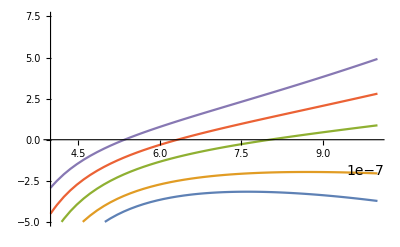

```mathematica
Plot[{ndiff[λ, 293, 7, 0,1, 0,1],ndiff[λ, 293, 6, 0,1, 0,2],ndiff[λ, 293, 5, 0,1, 0,3],ndiff[λ, 293, 4, 0,1, 1,3],ndiff[λ, 293, 3, 0,1, 2,3]},{λ, 400*10^(-9) , 1000*10^(-9)}, PlotRange->{{ 400*10^(-9) , 1000*10^(-9)},{-5,7.5}}]
```

## If we would leave the indices unchanged, the results do not match the plots from the given paper.

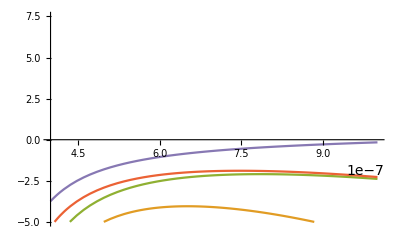

```mathematica
Plot[{ndiff[λ, 293, 7, 1,1, 1,1],ndiff[λ, 293, 6, 1,1, 1,2],ndiff[λ, 293, 5, 1,1, 1,3],ndiff[λ, 293, 4, 1,1, 1,3],ndiff[λ, 293, 3, 1,1, 2,3]},{λ, 400*10^(-9) , 1000*10^(-9)}, PlotRange->{{ 400*10^(-9) , 1000*10^(-9)},{-5,7.5}}]
```

## Pressure needed for third harmonic generation using Krypton

```mathematica
B1Kr:=26102.88*10^(-8)
C1Kr:=2.01*10^(-6)*(1*10^(-6))^2
B2Kr:=56946.82*10^(-8)
C2Kr:=10.043*10^(-3)*(1*10^(-6))^2
λ:=800*10^(-9)
nKr[λ_, T_, p_, m_, l_]:=Sqrt[1+δ[λ,T,B1Kr, C1Kr, B2Kr, C2Kr]*p/p0-(BesselJZero[m,l]/k[λ ]/a)^2]
ndiffKr[λ_, T_, p_, m1_, n1_, m2_,n2_]:=10^4*(nKr[λ, T, p, m1,n1]-nKr[λ/3, T, p, m2,n2])
```

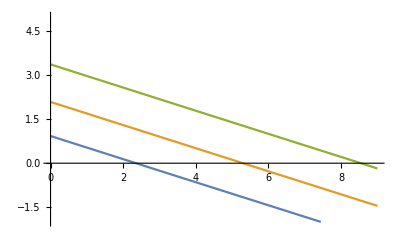

```mathematica
Plot[{ndiffKr[λ, 293,p, 0,1, 0,3],ndiffKr[λ, 293, p, 0,1, 1,3],ndiffKr[λ, 293, p, 0,1, 2,3]},{p,0,9}, PlotRange->{{0,9},{-2,5}}]
```

## Third harmonics generation with Xenon

```mathematica
B1Xe:=103701.61*10^(-8)
C1Xe:=12.75*10^3*10^(-6)*(1*10^(-6))^2
B2Xe:=31228.61*10^(-8)
C2Xe:=0.561*10^(-3)*(1*10^(-6))^2
λ:=800*10^(-9)
p:=0.96
nXe[λ_, T_, p_, m_, l_]:=Sqrt[1+δ[λ,T,B1Xe, C1Xe, B2Xe, C2Xe]*p/p0-(BesselJZero[m,l]/k[λ ]/a)^2]
ndiffXe[λ_, T_, p_, m1_, n1_, m2_,n2_]:=10^4*(nXe[λ, T, p, m1,n1]-nXe[λ/3, T, p, m2,n2])
```

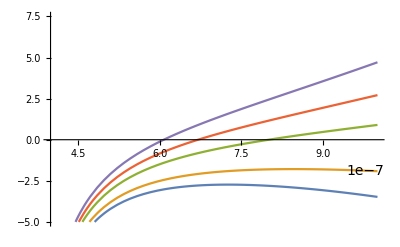

```mathematica
Plot[{ndiffXe[λ, 293, p, 0,1, 0,1],ndiffXe[λ, 293, p, 0,1, 0,2],ndiffXe[λ, 293, p, 0,1, 0,3],ndiffXe[λ, 293, p, 0,1, 1,3],ndiffXe[λ, 293,p, 0,1, 2,3]},{λ, 400*10^(-9) , 1000*10^(-9)}, PlotRange->{{ 400*10^(-9) , 1000*10^(-9)},{-5,7.5}}]
```